# pivotal MeSH

## PMID to MeSH rule

```mathematica
AbsoluteTiming[Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/mesh/PMIDtoMeSHDruleASC.save"];]
```

{130.349,Null}

```mathematica
PMIDtoMeSHDruleASC//Head
```

Association

## PMID vs pubyear

< year span >

```mathematica
yearrange=Partition[Table[ToString[n],{n,1946,2020}],5]
```

{{1946,1947,1948,1949,1950},{1951,1952,1953,1954,1955},{1956,1957,1958,1959,1960},{1961,1962,1963,1964,1965},{1966,1967,1968,1969,1970},{1971,1972,1973,1974,1975},{1976,1977,1978,1979,1980},{1981,1982,1983,1984,1985},{1986,1987,1988,1989,1990},{1991,1992,1993,1994,1995},{1996,1997,1998,1999,2000},{2001,2002,2003,2004,2005},{2006,2007,2008,2009,2010},{2011,2012,2013,2014,2015},{2016,2017,2018,2019,2020}}

< year span title >

```mathematica
yearrangetext=Map[#[[1]]<>"-"<>#[[5]]&,yearrange]
```

{1946-1950,1951-1955,1956-1960,1961-1965,1966-1970,1971-1975,1976-1980,1981-1985,1986-1990,1991-1995,1996-2000,2001-2005,2006-2010,2011-2015,2016-2020}

2 回目以降は以下を飛ばして下方のGetを実行する。

```mathematica
pubyearfiles=FileNames["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyear*X.wl"]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl00X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl01X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl02X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl03X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl04X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl05X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl06X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl07X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl08X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl09X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl10X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl11X.wl,/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearTbl12X.wl}

```mathematica
AbsoluteTiming[(pubyearList=Association[Flatten[Map[Import,pubyearfiles]]])//Length]
```

{39.3536,36551577}

```mathematica
AbsoluteTiming[Do[
pubyear[yearrangetext[[n]]]=Select[pubyearList,MemberQ[yearrange[[n]],#]&];,{n,15}
]]
```

{414.29,Null}

```mathematica
(*Save["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearrule.save",pubyear]*)
```

2 回目以降は以下をGetする

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/xml/element/pubyear/pubyearrule.save"];
```

## Total count of appearance of MeSH (各年 => 累積)

PMID (Key) の抽出

```mathematica
Do[
(pmidkey[yearrangetext[[n]]]=Keys[pubyear[yearrangetext[[n]]]])//Length,{n,15}
]
```

```mathematica
pmidkey[yearrangetext[[1]]][[1]]
```

12233288

PMIDからMeSHを引く

```mathematica
Do[
MeSHgenPre[yearrangetext[[n]]]=Map[PMIDtoMeSHDruleASC,pmidkey[yearrangetext[[n]]]],{n,15}
]
```

```mathematica
Table[Length[MeSHgenPre[yearrangetext[[n]]]],{n,15}]
```

{331362,534892,549642,725868,1014763,1166703,1352292,1542151,1917765,2144518,2393705,2971542,3776525,4953988,6062220}

```mathematica
MeSHgenPre["2016-2020"][[1]]
```

{Adolescent,Adult,Aged,Aged, 80 and over,Cheek,Coloring Agents,Ear Neoplasms,Facial Neoplasms,Facial Nerve,Facial Nerve Injuries,Female,Forehead,Humans,Lymph Node Excision,Lymphatic Metastasis,Lymphoscintigraphy,Male,Melanoma,Middle Aged,Neoplasm Recurrence, Local,Parotid Neoplasms,Parotid Region,Recovery of Function,Retrospective Studies,Sentinel Lymph Node,Sentinel Lymph Node Biopsy,Skin Neoplasms,Tumor Burden,Young Adult}

Missingをdrop

```mathematica
Do[
MeSHgen[yearrangetext[[n]]]=Cases[MeSHgenPre[yearrangetext[[n]]],x_/;Head[x]==List],{n,15}
]
```

```mathematica
Table[Length[MeSHgen[yearrangetext[[n]]]],{n,15}]
```

{319921,527332,538750,709330,987502,1138604,1317387,1484633,1813556,2002399,2229534,2777961,3434594,4190064,4479011}

### 延べカウント

<各世代のカウント>

```mathematica
MeSHflatcount=Table[Flatten[MeSHgen[yearrangetext[[n]]]]//Length,{n,15}]
```

{1260830,2405880,2550730,4831845,8429174,11935276,11955149,14373206,17562197,21776471,25912004,33165585,40830011,49634377,50404722}

<累積世代のカウント>

```mathematica
MeSHflatcountAcm=Accumulate[MeSHflatcount]
```

{1260830,3666710,6217440,11049285,19478459,31413735,43368884,57742090,75304287,97080758,122992762,156158347,196988358,246622735,297027457}

### タームカウント

各世代のTally

```mathematica
(MeSHflatcountTly=Table[Flatten[MeSHgen[yearrangetext[[n]]]]//Tally,{n,15}])//Length
```

15

```mathematica
MeSHflatcountTly[[1]]
```

累積世代のTally

```mathematica
tallyInteg[l_]:=If[Length[l]>=1,
{l[[1,1]],Total[Map[#[[2]]&,l]]},
l
]
```

```mathematica
(MeSHacmcountTly=Table[Map[tallyInteg,GatherBy[Apply[Join,MeSHflatcountTly[[1;;n]]],First]],{n,15}])//Length
```

15

<累積世代のディスクリプターのカウント>

```mathematica
MeSHDesccountAcm=Map[Length,MeSHacmcountTly]
```

{13448,15858,17483,19065,19489,20449,21492,22288,23304,24817,25954,27076,27881,28767,29898}

## Pivotal count of appearance of MeSH (各年 => 累積)

### 主要論文

変数: topCitingCitedArt1Perc[YYYY, "citing rule"]

```mathematica
mainartfiles=Table["/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-"<>ToString[n]<>"_topCitingCitedArt1Perc.save",{n,1950,2020,5}]
```

{/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1950_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1955_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1960_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1965_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1970_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1975_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1980_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1985_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1990_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-1995_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2000_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2005_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2010_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2015_topCitingCitedArt1Perc.save,/Volumes/elecom/BANK/pubmed/202312/xml/element/reference/1946-2020_topCitingCitedArt1Perc.save}

```mathematica
Map[Get,mainartfiles];
```

```mathematica
mainartPMIDgen=Table[Map[#[[2]]&,topCitingCitedArt1Perc[n, "citing rule"],{2}]//Flatten//Union,{n,1950,2020,5}];
```

```mathematica
mainartPMIDgen[[2,1]]
```

14772207

```mathematica
PMIDtoMeSHDruleASC[mainartPMIDgen[[2,1]]]
```

{Blood Proteins,Electrophoresis,Filtration}

### 主要MeSH

PMIDからMeSHを引く

```mathematica
(mainMeSHgen=DeleteCases[Map[PMIDtoMeSHDruleASC,mainartPMIDgen,{-1}],_Missing,Infinity])//Length
```

15

```mathematica
mainMeSHgen[[2]]//Flatten//Tally
```

{{Blood Proteins,2},{Electrophoresis,2},{Filtration,2},{Blood,1},{Proteins,2},{Molybdenum,1},{Phenols,1},{Plant Extracts,1},{Tungsten Compounds,1},{Anemia,1},{Anemia, Sickle Cell,1},{Humans,6},{Chromatography,2},{Chromatography, Paper,2},{Esters,1},{Phosphorus,1},{Phosphorus Compounds,1},{Rare Diseases,1},{Salts,1},{Acclimatization,1},{Adaptation, Physiological,1},{Metabolic Networks and Pathways,1},{Metabolism,1},{Brain,1},{Cerebrovascular Circulation,1},{Male,1},{Nitrous Oxide,1},{Reference Values,1},{Cytochromes,1},{Cytochromes c,1},{Insulin,1},{Complex Mixtures,1},{Identification, Psychological,1},{Peptides,1},{Adrenal Glands,1},{Epinephrine,1},{Tissue Extracts,1},{Capillaries,1},{Animals,1},{Axons,1},{Decapodiformes,1},{Ions,1},{Neurons,1},{Sodium,1},{Sodium, Dietary,1}}

### 延べカウント

```mathematica
mainMeSHflatcountAcm=Map[Length[Flatten[#]]&,mainMeSHgen]
```

{0,56,139,192,194,189,199,220,162,202,321,637,2008,3462,3613}

### タームカウント

```mathematica
mainMeSHgen[[2]]
```

{{Blood Proteins,Electrophoresis,Filtration},{Blood,Blood Proteins,Electrophoresis,Proteins},{Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds},{Anemia,Anemia, Sickle Cell,Humans},{Chromatography,Chromatography, Paper,Esters,Filtration,Phosphorus,Phosphorus Compounds,Rare Diseases},{Humans,Salts},{Acclimatization,Adaptation, Physiological,Humans,Metabolic Networks and Pathways,Metabolism},{Brain,Cerebrovascular Circulation,Humans,Male,Nitrous Oxide,Reference Values},{Cytochromes,Cytochromes c},{Insulin},{Complex Mixtures,Humans,Identification, Psychological,Peptides},{Adrenal Glands,Epinephrine,Tissue Extracts},{Capillaries,Chromatography,Chromatography, Paper,Humans},{Animals,Axons,Decapodiformes,Ions,Neurons,Sodium,Sodium, Dietary}}

```mathematica
(mainMeSHflatcountTly=Map[Tally[Flatten[#]]&,mainMeSHgen])//Length
```

15

```mathematica
mainMeSHflatcountTly[[5]]
```

{{Axons,2},{Humans,9},{Immune Sera,2},{Kidney,1},{Male,1},{Poliomyelitis,1},{Poliovirus,1},{Testis,1},{Virion,1},{Viruses,1},{Cytoplasm,2},{Enzymes,3},{Liver,2},{Electrophoresis,3},{Immunoelectrophoresis,1},{Blood Proteins,2},{Gels,1},{Starch,1},{Blood,1},{Fatty Acids,1},{Fatty Acids, Nonesterified,1},{Glucose,1},{Plasma,1},{Amines,1},{Colorimetry,1},{DNA,2},{Diphenylamine,1},{Nucleic Acids,1},{Lipids,1},{Coloring Agents,6},{Staining and Labeling,7},{Tissue Fixation,1},{Electrons,8},{Metals,1},{Metals, Heavy,1},{Microscopy,8},{Microscopy, Electron,9},{Plants, Medicinal,1},{Bacteria,2},{Bacteriophages,1},{Cell Nucleus,1},{Escherichia coli,2},{Organelles,1},{Biological Assay,1},{Chromatography,3},{Phosphorus,2},{Transaminases,1},{Amino Acids,1},{Animals,4},{Cell Culture Techniques,1},{Mammals,1},{Tissue Culture Techniques,1},{Chromosomes,2},{Proteins,4},{Epoxy Resins,1},{Histological Techniques,3},{Resins, Plant,1},{Resins, Synthetic,1},{Leukocytes,1},{Cell Membrane,1},{Colon,1},{Desmosomes,1},{Epithelial Cells,1},{Epithelium,1},{Female,1},{Gallbladder,1},{Guinea Pigs,1},{Jejunum,1},{Kidney Tubules,1},{Oviducts,1},{Pancreas,1},{Parotid Gland,1},{Rats,1},{Stomach,1},{Thyroid Gland,1},{Tight Junctions,1},{Uterus,1},{Aldehydes,1},{Cell Biology,1},{Histocytochemistry,1},{Osmium,1},{Citrates,2},{Citric Acid,2},{Lead,2},{Blood Protein Electrophoresis,1},{Buffers,1},{Electrophoresis, Disc,1},{Equipment and Supplies,1},{Hydrogen-Ion Concentration,1},{Indicators and Reagents,1},{Nuclear Receptor Subfamily 4, Group A, Member 2,1},{Research,2},{Microtomy,1},{Carbohydrates,1},{Chromatography, Paper,2},{Adsorption,1},{Antibodies,2},{Antigens,2},{Erythrocytes,1},{Hemagglutination,1},{Hemagglutination Tests,1},{Sheep,1},{Tannins,1},{Molybdenum,1},{Phenols,1},{Plant Extracts,1},{Tungsten Compounds,1},{Histology,1},{Fluorescent Antibody Technique,1},{Immunoglobulins,1},{Esters,1},{Filtration,1},{Phosphorus Compounds,1},{Rare Diseases,1},{Corrinoids,1},{Methionine,1},{Vitamin B 12,1},{Decapodiformes,1},{Ions,1},{Neurons,1},{Sodium,1},{Sodium, Dietary,1}}

```mathematica
mainMeSHgencount=Map[Length,mainMeSHflatcountTly]
```

{0,45,96,117,122,125,137,143,108,128,199,325,875,1243,1178}

### 新規出現

すでに累積になっているので前世代との差分をとる。

```mathematica
mainMeSHgenflatt=Map[Flatten[#]&,mainMeSHgen];
```

```mathematica
mainMeSHgendiff=Table[Complement[mainMeSHgenflatt[[n+1]],mainMeSHgenflatt[[n]]],{n,14}];
```

```mathematica
mainMeSHgennewcomercount=Prepend[Map[Length,mainMeSHgendiff],0]
```

{0,45,61,42,33,21,44,55,9,30,71,126,550,468,217}

```mathematica
Complement[{"a","a","b"},{"b"}]
```

{a}

### 複数の世代で出現するターム

< 最初の世代を除くすべてで出現 >

```mathematica
Apply[Intersection,mainMeSHgenflatt[[2;;15]]]
```

{Animals,Electrophoresis,Humans,Molybdenum,Phenols,Plant Extracts,Proteins,Tungsten Compounds}

< タームごとの出現世代数 >

```mathematica
SortBy[Map[Union,mainMeSHgenflatt]//Flatten//Tally,-#[[2]]&]
```

{{Animals,14},{Electrophoresis,14},{Humans,14},{Molybdenum,14},{Phenols,14},{Plant Extracts,14},{Proteins,14},{Tungsten Compounds,14},{Antigens,13},{Electrons,13},{Escherichia coli,13},{Microscopy,13},{Microscopy, Electron,13},{Blood Proteins,12},{Citrates,12},{Citric Acid,12},{Colorimetry,12},{Coloring Agents,12},{DNA,12},{Gels,12},{Histological Techniques,12},{Lead,12},{Lipids,12},{Liver,12},{Methionine,12},{Nucleic Acids,12},{Staining and Labeling,12},{Electrophoresis, Disc,11},{Epoxy Resins,11},{Hydrogen-Ion Concentration,11},{Peptides,11},{Phosphorus,11},{Rats,11},{Resins, Plant,11},{Resins, Synthetic,11},{RNA,11},{Acrylates,10},{Amines,10},{Amino Acids,10},{Axons,10},{Buffers,10},{Chemical Phenomena,10},{Chemistry,10},{Chromatography,10},{Cytoplasm,10},{Detergents,10},{Diphenylamine,10},{Indicators and Reagents,10},{Male,10},{Methods,10},{Molecular Weight,10},{Rabbits,10},{Research,10},{Sodium,10},{Sulfates,10},{Time Factors,10},{Autoradiography,9},{Base Sequence,9},{Blood Protein Electrophoresis,9},{Carbon Isotopes,9},{Coliphages,9},{Electrophoresis, Polyacrylamide Gel,9},{Equipment and Supplies,9},{Genes,9},{Genetics, Microbial,9},{Histocytochemistry,9},{Kidney,9},{Kinetics,9},{Mice,9},{Nuclear Receptor Subfamily 4, Group A, Member 2,9},{Nucleic Acid Hybridization,9},{Oligodeoxyribonucleotides,9},{Osmolar Concentration,9},{Pancreas,9},{Sepharose,9},{Species Specificity,9},{Viral Proteins,9},{Adsorption,8},{Antigen-Antibody Reactions,8},{Bacteria,8},{Bacterial Proteins,8},{Binding Sites,8},{Cellulose,8},{Chickens,8},{Chromatography, Ion Exchange,8},{Chromosomes, Bacterial,8},{Cloning, Molecular,8},{Deoxyribonucleotides,8},{DNA, Circular,8},{DNA-Directed DNA Polymerase,8},{DNA Polymerase I,8},{DNA, Recombinant,8},{DNA Restriction Enzymes,8},{DNA, Single-Stranded,8},{DNA, Viral,8},{Electrophoresis, Agar Gel,8},{Erythrocytes,8},{Genetic Techniques,8},{Immunologic Techniques,8},{Isoelectric Focusing,8},{Isotope Labeling,8},{Membranes,8},{Microchemistry,8},{Muscles,8},{Nucleic Acid Denaturation,8},{Phosphorus Radioisotopes,8},{Plasmids,8},{Polynucleotide 5'-Hydroxyl-Kinase,8},{Protein Binding,8},{Ribosomal Proteins,8},{Rosaniline Dyes,8},{Sodium Dodecyl Sulfate,8},{T-Phages,8},{Transformation, Bacterial,8},{Biological Assay,7},{Chick Embryo,7},{Chromosome Mapping,7},{Collodion,7},{Cytidine Triphosphate,7},{Dimethyl Sulfoxide,7},{Enzymes,7},{Fishes,7},{Hot Temperature,7},{Leukocytes,7},{Mammals,7},{Protein Biosynthesis,7},{Reticulocytes,7},{Ribonucleases,7},{RNA, Messenger,7},{Serum Albumin,7},{Solutions,7},{Templates, Genetic,7},{Transaminases,7},{Acetylcholine,6},{Biochemistry,6},{Carbon Radioisotopes,6},{Cattle,6},{Cell Line,6},{Cell Membrane,6},{Cell Nucleus,6},{Chloroform,6},{Computers,6},{Conjugation, Genetic,6},{Electrophysiology,6},{Fetus,6},{Film Dosimetry,6},{Filtration,6},{Genetic Vectors,6},{Globins,6},{Guanidine,6},{Guanidines,6},{Immunodiffusion,6},{Immunoglobulins,6},{Information Systems,6},{Insulin,6},{In Vitro Techniques,6},{Ion Channels,6},{Ions,6},{Kidney Tubules,6},{Mammary Glands, Animal,6},{Methylation,6},{Mutation,6},{Neurons,6},{Nucleic Acid Amplification Techniques,6},{Nucleic Acid Conformation,6},{Phenol,6},{Plants,6},{Rana temporaria,6},{Rare Diseases,6},{Receptors, Cholinergic,6},{Recombination, Genetic,6},{Software,6},{Sulfur Radioisotopes,6},{Thermus,6},{Tritium,6},{Adenine,5},{Adenoviridae,5},{Algorithms,5},{Amino Acid Sequence,5},{Bacteriorhodopsins,5},{Biochemical Phenomena,5},{Biological Transport,5},{Blood,5},{Brain,5},{Calcium Chloride,5},{Carcinoma,5},{Cell Culture Techniques,5},{Cell Differentiation,5},{Cells, Cultured,5},{Centrifugation,5},{Chromatography, Paper,5},{Chymotrypsinogen,5},{Corrinoids,5},{Cytosine,5},{Databases, Factual,5},{Deoxyribonucleases,5},{Dextrans,5},{DNA, Bacterial,5},{DNA-Directed RNA Polymerases,5},{Dose-Response Relationship, Drug,5},{Esters,5},{Female,5},{Gene Expression Regulation,5},{Guanine,5},{HeLa Cells,5},{Histology,5},{Hydrazines,5},{Immune Sera,5},{L-Lactate Dehydrogenase,5},{Magnesium,5},{Membrane Proteins,5},{Mouth Neoplasms,5},{Operon,5},{Peroxidases,5},{Phosphorus Compounds,5},{Plants, Edible,5},{Poliomyelitis,5},{Poliovirus,5},{Protease Inhibitors,5},{Repetitive Sequences, Nucleic Acid,5},{RNA, Neoplasm,5},{RNA Polymerase II,5},{RNA, Transfer,5},{Saccharomyces cerevisiae,5},{Sensitivity and Specificity,5},{Sequence Homology, Nucleic Acid,5},{Solubility,5},{Temperature,5},{Testis,5},{Thymine,5},{Thymus Gland,5},{Tissue Culture Techniques,5},{Transcription, Genetic,5},{Transformation, Genetic,5},{Vegetables,5},{Viral Plaque Assay,5},{Virion,5},{Viruses,5},{Viscosity,5},{Vitamin B 12,5},{Water,5},{Absorption,4},{Acetyltransferases,4},{Aldehydes,4},{Aminoquinolines,4},{Bacteriophage lambda,4},{Bacteriophages,4},{Benzofurans,4},{Biological Evolution,4},{Biometry,4},{Calcium,4},{Cations,4},{Cations, Monovalent,4},{Cell Biology,4},{Centromere,4},{Cerebrovascular Circulation,4},{Chemistry, Physical,4},{Chloramphenicol O-Acetyltransferase,4},{Chlorocebus aethiops,4},{Cholesterol,4},{Chromosomes,4},{Computer Graphics,4},{Crystallization,4},{Culture Media,4},{Decapodiformes,4},{Dithiothreitol,4},{DNA, Fungal,4},{DNA, Superhelical,4},{DNA Transposable Elements,4},{Drosophila melanogaster,4},{Epithelial Cells,4},{Erythrocyte Membrane,4},{Flow Cytometry,4},{Fluorescent Dyes,4},{Fura-2,4},{Gene Expression,4},{Genetic Engineering,4},{Genetic Linkage,4},{Genotype,4},{Glucose,4},{Hydrolases,4},{Immunity,4},{Immunoelectrophoresis,4},{Indoles,4},{Lithium,4},{Mathematics,4},{Metals,4},{Metals, Heavy,4},{Mice, Inbred BALB C,4},{Mitochondria,4},{Models, Genetic,4},{Models, Molecular,4},{Molecular Biology,4},{Molecular Sequence Data,4},{Molecular Structure,4},{Osmium,4},{Phenotype,4},{Phylogeny,4},{Plants, Medicinal,4},{Polyethylene Glycols,4},{Potassium,4},{Promoter Regions, Genetic,4},{Protein Structure, Secondary,4},{Quinolines,4},{Ranidae,4},{Reference Values,4},{Regression Analysis,4},{Restriction Mapping,4},{RNA, Ribosomal,4},{Rubidium,4},{Sequence Alignment,4},{Sodium, Dietary,4},{Spectrometry, Fluorescence,4},{Spectrophotometry,4},{Stilbenes,4},{Terminology as Topic,4},{Thiobarbiturates,4},{X-Ray Diffraction,4},{Acrylamides,3},{Activities of Daily Living,3},{Actuarial Analysis,3},{Adaptation, Physiological,3},{Adolescent,3},{Adrenal Glands,3},{Adrenergic alpha-Agonists,3},{Adrenergic alpha-Antagonists,3},{Adult,3},{Affective Symptoms,3},{Aged,3},{Aged, 80 and over,3},{Age Distribution,3},{Age Factors,3},{Alleles,3},{Alzheimer Disease,3},{Amino Acid Motifs,3},{Ampicillin,3},{Anemia, Sickle Cell,3},{Angiotensin-Converting Enzyme Inhibitors,3},{Angiotensin Receptor Antagonists,3},{Antibodies,3},{Antibody Formation,3},{Antibody Specificity,3},{Antigen Presentation,3},{Antigens, Viral,3},{Antihypertensive Agents,3},{Antineoplastic Agents,3},{Anxiety Disorders,3},{Apoptosis,3},{Arabidopsis,3},{Arteriosclerosis,3},{Arthritis, Rheumatoid,3},{Attitude,3},{Automation,3},{Avidin,3},{Bayes Theorem,3},{Behavior,3},{Biomarkers, Tumor,3},{Biotin,3},{Bipolar Disorder,3},{Blood Cell Count,3},{Blood Cells,3},{Blood Glucose,3},{Blood Platelets,3},{Blood Pressure,3},{Blood Pressure Determination,3},{Blood Pressure Monitors,3},{Blood Protein Disorders,3},{Blood Sedimentation,3},{B-Lymphocytes,3},{Body Mass Index,3},{Breast Neoplasms,3},{Caenorhabditis elegans,3},{Caenorhabditis elegans Proteins,3},{Calcium Channel Blockers,3},{Calmodulin-Binding Proteins,3},{Capsid,3},{Carbohydrates,3},{Carcinoma, Krebs 2,3},{Cardiovascular Diseases,3},{Case-Control Studies,3},{Cause of Death,3},{Cell Cycle,3},{Cell-Free System,3},{Cell Fusion,3},{Cell Movement,3},{Cells,3},{Cell Survival,3},{Cell Transformation, Neoplastic,3},{Centrifugation, Density Gradient,3},{Chemical Precipitation,3},{Child,3},{Child, Preschool,3},{Chloramphenicol,3},{Chlorpropamide,3},{Cholesterol, HDL,3},{Cholesterol, LDL,3},{Chromatin,3},{Chromatography, Gel,3},{Chromosomes, Artificial, Bacterial,3},{Chromosomes, Human,3},{Chromosomes, Human, Y,3},{Clinical Trials as Topic,3},{Cluster Analysis,3},{Cognition,3},{Cognition Disorders,3},{Computational Biology,3},{Computer Communication Networks,3},{Computer Simulation,3},{Concanavalin A,3},{Confidence Intervals,3},{Conserved Sequence,3},{Contrast Media,3},{Coronary Artery Disease,3},{Coronary Disease,3},{CpG Islands,3},{Craniocerebral Trauma,3},{Crohn Disease,3},{Cross-Cultural Comparison,3},{Crosses, Genetic,3},{Crystallography, X-Ray,3},{Culture,3},{Culture Techniques,3},{Cytotoxicity Tests, Immunologic,3},{Database Management Systems,3},{Databases, Genetic,3},{Databases, Nucleic Acid,3},{Data Display,3},{Data Interpretation, Statistical,3},{Dementia,3},{Dendritic Cells,3},{Depression,3},{Depressive Disorder,3},{Diabetes Mellitus,3},{Diabetes Mellitus, Type 1,3},{Diabetes Mellitus, Type 2,3},{Diabetic Angiopathies,3},{Diabetic Nephropathies,3},{Diabetic Neuropathies,3},{Diabetic Retinopathy,3},{Diagnosis,3},{Diagnosis, Differential,3},{Diagnostic Tests, Routine,3},{Diet, Fat-Restricted,3},{Diet, Reducing,3},{Disease-Free Survival,3},{Diuretics,3},{DNA, Complementary,3},{DNA Damage,3},{DNA Glycosylases,3},{DNA, Mitochondrial,3},{DNA Nucleotidyltransferases,3},{DNA Primers,3},{DNA Probes,3},{DNA Repair,3},{DNA, Ribosomal,3},{Dose-Response Relationship, Immunologic,3},{Down-Regulation,3},{Drosophila,3},{Drug Industry,3},{Drug Resistance, Microbial,3},{Edetic Acid,3},{Educational Status,3},{Electrophoresis, Paper,3},{Endoscopy,3},{Endothelium, Vascular,3},{Enhancer Elements, Genetic,3},{Epidemiologic Methods,3},{Epidemiologic Studies,3},{Erythrocyte Count,3},{Ethnicity,3},{Eukaryotic Cells,3},{Evaluation Studies as Topic,3},{Evolution, Molecular,3},{Exercise,3},{Exons,3},{Eye,3},{Fasting,3},{Fatty Acids,3},{Fatty Acids, Nonesterified,3},{Fluorescent Antibody Technique,3},{Follow-Up Studies,3},{Forecasting,3},{Functional Laterality,3},{GC Rich Sequence,3},{Gene Duplication,3},{Gene Expression Profiling,3},{Gene Expression Regulation, Neoplastic,3},{Gene Frequency,3},{Genes, Bacterial,3},{Genes, Dominant,3},{Genes, Helminth,3},{Genes, Lethal,3},{Genes, Tumor Suppressor,3},{Genes, Viral,3},{Genetic Code,3},{Genetic Complementation Test,3},{Genetic Diseases, Inborn,3},{Genetic Markers,3},{Genetic Predisposition to Disease,3},{Genetics, Behavioral,3},{Genetics, Medical,3},{Genetics, Population,3},{Genetic Variation,3},{Genome,3},{Genome, Bacterial,3},{Genome, Fungal,3},{Genome, Human,3},{Genomics,3},{Geography,3},{Glipizide,3},{Global Health,3},{Glucuronidase,3},{Glyburide,3},{Glycated Hemoglobin,3},{Haplotypes,3},{Health Policy,3},{Health Services Research,3},{Health Status,3},{Health Surveys,3},{Helminth Proteins,3},{Hemagglutination,3},{Hemagglutination Tests,3},{Hematology,3},{Heparin,3},{Histones,3},{Homeodomain Proteins,3},{Homeostasis,3},{Human Genome Project,3},{Hydrogen Bonding,3},{Hypercholesterolemia,3},{Hyperhomocysteinemia,3},{Hyperlipidemias,3},{Hypertension,3},{Hypoglycemic Agents,3},{Hypolipidemic Agents,3},{Immunoenzyme Techniques,3},{Immunoglobulin Heavy Chains,3},{Incidence,3},{Infant,3},{Infant, Newborn,3},{Inflammation,3},{Information Storage and Retrieval,3},{Insulin Infusion Systems,3},{Insulin Resistance,3},{Integrases,3},{Interleukin-2,3},{International Cooperation,3},{Internet,3},{Interview, Psychological,3},{Introns,3},{Islets of Langerhans,3},{Kallikreins,3},{Kanamycin,3},{Kidney Diseases,3},{Lac Operon,3},{Leucine,3},{Leukemia Virus, Murine,3},{Leukocyte Count,3},{Life Style,3},{Ligands,3},{Likelihood Functions,3},{Linear Models,3},{Linkage Disequilibrium,3},{Lipopolysaccharides,3},{Lipoproteins,3},{Lipoproteins, HDL,3},{Lipoproteins, LDL,3},{Lipoproteins, VLDL,3},{Longitudinal Studies,3},{Lymphocyte Activation,3},{Lymphocytes,3},{Lymphoma,3},{Macromolecular Substances,3},{Macrophage Activation,3},{Magnetic Resonance Spectroscopy,3},{Markov Chains,3},{Mental Disorders,3},{Mental Health,3},{Mental Status Schedule,3},{Mesylates,3},{Metabolic Diseases,3},{Metaphysics,3},{Mice, Transgenic,3},{Microcomputers,3},{MicroRNAs,3},{Microscopy, Electron, Scanning,3},{Middle Aged,3},{Models, Biological,3},{Models, Psychological,3},{Models, Statistical,3},{Models, Theoretical,3},{Monocytes,3},{Morbidity,3},{Motor Activity,3},{Motor Skills,3},{Movement,3},{Multigene Family,3},{Multiple Myeloma,3},{Multiple Sclerosis,3},{Muscle Proteins,3},{Muscle, Skeletal,3},{Muscle, Smooth, Vascular,3},{Mutagenesis,3},{Mutagenesis, Insertional,3},{Nematoda,3},{Neoplasm Proteins,3},{Neoplasms,3},{Neoplasms, Experimental,3},{Neoplasm Staging,3},{Neovascularization, Pathologic,3},{Nervous System Physiological Phenomena,3},{Neurotic Disorders,3},{Neutrophils,3},{New York City,3},{N-Glycosyl Hydrolases,3},{Normal Distribution,3},{Nucleotides,3},{Nutrition Surveys,3},{Obesity,3},{Oligonucleotide Array Sequence Analysis,3},{Online Systems,3},{Outcome Assessment, Health Care,3},{Outpatient Clinics, Hospital,3},{Outpatients,3},{Ovalbumin,3},{Overweight,3},{Oviducts,3},{Pancreatic Elastase,3},{Patients,3},{Peak Expiratory Flow Rate,3},{Personality,3},{Personality Inventory,3},{Phagocytosis,3},{Phospholipids,3},{Physical Chromosome Mapping,3},{Plant Proteins,3},{Plants, Genetically Modified,3},{Plant Stems,3},{Plasma,3},{Polymerase Chain Reaction,3},{Polymorphism, Genetic,3},{Polymorphism, Single Nucleotide,3},{Polynucleotides,3},{Polyomavirus,3},{Polysaccharides,3},{Population Surveillance,3},{Prevalence,3},{Private Sector,3},{Probability,3},{Prognosis,3},{Programming Languages,3},{Prospective Studies,3},{Protein Conformation,3},{Protein Sorting Signals,3},{Protein Structure, Tertiary,3},{Proteome,3},{Psychiatric Status Rating Scales,3},{Psychological Tests,3},{Psychology, Social,3},{Psychometrics,3},{Public Sector,3},{Quantitative Trait Loci,3},{Racial Groups,3},{Radiation, Ionizing,3},{Radiography,3},{Receptor, Insulin,3},{Receptors, Antigen, T-Cell,3},{Recombinases,3},{Reference Standards,3},{Regulatory Sequences, Nucleic Acid,3},{Reproducibility of Results,3},{Reproduction,3},{Research Design,3},{Retrospective Studies,3},{Reverse Transcriptase Polymerase Chain Reaction,3},{Rheumatology,3},{Rhizobium,3},{Ribulose-Bisphosphate Carboxylase,3},{Risk,3},{Risk Assessment,3},{Risk Factors,3},{Risk Reduction Behavior,3},{RNA, Antisense,3},{RNA, Bacterial,3},{RNA, Double-Stranded,3},{RNA, Small Interfering,3},{RNA, Viral,3},{Role,3},{Saline Solution, Hypertonic,3},{Salmonella Phages,3},{Salmonella typhimurium,3},{Sampling Studies,3},{Schizophrenia,3},{Selection, Genetic,3},{Self-Assessment,3},{Self Tolerance,3},{Sequence Analysis, DNA,3},{Sequence Analysis, Protein,3},{Sequence Homology,3},{Sequence Homology, Amino Acid,3},{Sex Chromosomes,3},{Sex Distribution,3},{Sex Factors,3},{Sheep,3},{Signal Transduction,3},{Silicones,3},{Societies, Medical,3},{Socioeconomic Factors,3},{Solvents,3},{Spectinomycin,3},{Spleen,3},{Staphylococcal Protein A,3},{Starch,3},{Statistics as Topic,3},{Statistics, Nonparametric,3},{Stochastic Processes,3},{Substance-Related Disorders,3},{Sulfhydryl Compounds,3},{Sulfonylurea Compounds,3},{Surveys and Questionnaires,3},{Survival Analysis,3},{Survival Rate,3},{Tannins,3},{Tetracycline,3},{Tetrazolium Salts,3},{Thermodynamics,3},{Thiazoles,3},{Thymidine,3},{Thymine Nucleotides,3},{Tissue Kallikreins,3},{T-Lymphocytes,3},{Tomography, Emission-Computed,3},{Tomography, X-Ray Computed,3},{Transcription Factors,3},{Transduction, Genetic,3},{Transfection,3},{Transforming Growth Factors,3},{Treatment Outcome,3},{Triglycerides,3},{Trypsin,3},{Tumor Cells, Cultured,3},{Tumor Suppressor Protein p53,3},{Ultracentrifugation,3},{Ultrasonography,3},{United Kingdom,3},{United States,3},{United States Dept. of Health and Human Services,3},{Up-Regulation,3},{Uracil,3},{Uracil-DNA Glycosidase,3},{User-Computer Interface,3},{Vasodilator Agents,3},{3' Untranslated Regions,2},{Acetylation,2},{Acoustic Stimulation,2},{Acute Disease,2},{Adenocarcinoma,2},{Adenosine,2},{Adenosine Triphosphate,2},{Adipocytes,2},{Adrenal Cortex Hormones,2},{Adult Stem Cells,2},{Age of Onset,2},{Albumins,2},{Alternative Splicing,2},{American Cancer Society,2},{Amino Acid Substitution,2},{Amyloid,2},{Amyloid beta-Peptides,2},{Amyloid beta-Protein Precursor,2},{Anemia,2},{Anions,2},{Antennapedia Homeodomain Protein,2},{Anthropometry,2},{Antibodies, Monoclonal,2},{Anticholesteremic Agents,2},{Antigens, CD,2},{Antigens, Nuclear,2},{Antigens, Tumor-Associated, Carbohydrate,2},{Anti-Inflammatory Agents,2},{Antineoplastic Agents, Alkylating,2},{Aprotinin,2},{Aquaporins,2},{Archaeal Proteins,2},{Arousal,2},{Arthritis,2},{Attention,2},{Automation, Laboratory,2},{Bacterial Typing Techniques,2},{Bacteriophage P1,2},{Barbiturates,2},{Base Composition,2},{Bias,2},{Binding, Competitive,2},{Binomial Distribution,2},{Biodiversity,2},{Biomarkers,2},{Blastocyst,2},{Blood Vessels,2},{Bone and Bones,2},{Bone Marrow Cells,2},{Brain Chemistry,2},{Brain Mapping,2},{Brain Neoplasms,2},{Caenorhabditis,2},{Calibration,2},{California,2},{Cancer Vaccines,2},{Carbon Tetrachloride,2},{Carcinoma, Ductal, Breast,2},{Carcinoma in Situ,2},{Carcinoma, Lobular,2},{Carcinoma, Non-Small-Cell Lung,2},{CD24 Antigen,2},{Cell Adhesion,2},{Cell Cycle Proteins,2},{Cell Division,2},{Cell Lineage,2},{Cell Line, Tumor,2},{Cell Proliferation,2},{Cell Separation,2},{Cell Shape,2},{Cell Transplantation,2},{Cellular Reprogramming,2},{Cell Wall,2},{Central Nervous System Neoplasms,2},{Cerebral Cortex,2},{Chemokines,2},{Chemotherapy, Adjuvant,2},{Chi-Square Distribution,2},{Chlamydia Infections,2},{Chloramines,2},{Chlorine,2},{Chloroplasts,2},{Chondrocytes,2},{Chromatin Assembly and Disassembly,2},{Chromatin Immunoprecipitation,2},{Chromosome Banding,2},{Chromosomes, Mammalian,2},{Chronic Disease,2},{Cleavage Stage, Ovum,2},{Clinical Laboratory Techniques,2},{Cnidaria,2},{Cohort Studies,2},{Coleoptera,2},{Colon,2},{Colorectal Neoplasms,2},{Combined Modality Therapy,2},{Communicable Diseases,2},{Communication,2},{Comorbidity,2},{Computer Systems,2},{Computer Terminals,2},{Consensus Sequence,2},{Contraceptives, Oral,2},{Cooperative Behavior,2},{Coronary Artery Bypass,2},{COS Cells,2},{Cost of Illness,2},{Costs and Cost Analysis,2},{Cotinine,2},{Creatinine,2},{Critical Care,2},{Cross-Sectional Studies,2},{Cryopreservation,2},{Crystallography,2},{CTLA-4 Antigen,2},{Cyclic AMP Receptor Protein,2},{Cytidine Diphosphate Choline,2},{Cytokines,2},{Cytoskeleton,2},{Dacarbazine,2},{Databases as Topic,2},{Databases, Protein,2},{Data Mining,2},{Deoxyribonuclease I,2},{Desmosomes,2},{Diagnosis, Computer-Assisted,2},{Diagnosis-Related Groups,2},{Diagnostic and Statistical Manual of Mental Disorders,2},{Diet,2},{Diet Therapy,2},{Dimerization,2},{Disease,2},{Disease Management,2},{Disease Progression,2},{DNA-Binding Proteins,2},{DNA Footprinting,2},{DNA, Intergenic,2},{DNA Methylation,2},{DNA Modification Methylases,2},{DNA Mutational Analysis,2},{DNA, Neoplasm,2},{DNA, Plant,2},{DNA Repair Enzymes,2},{DNA Replication,2},{Dogs,2},{Dominance, Cerebral,2},{Double-Blind Method,2},{Drug Resistance, Neoplasm,2},{Drug Therapy,2},{Echo-Planar Imaging,2},{Ectoderm,2},{Electrodes,2},{Electroencephalography,2},{Electronic Data Processing,2},{Electrophoresis, Gel, Pulsed-Field,2},{Embryo, Mammalian,2},{Embryonic Stem Cells,2},{Embryo, Nonmammalian,2},{Encyclopedias as Topic,2},{Endoderm,2},{Endoplasmic Reticulum,2},{Energy Intake,2},{England,2},{Entropy,2},{Environmental Microbiology,2},{Enzyme Activation,2},{Enzyme Inhibitors,2},{Epidermal Growth Factor,2},{Epigenesis, Genetic,2},{Epinephrine,2},{Epithelium,2},{ErbB Receptors,2},{Escherichia coli Proteins,2},{Europe,2},{Evoked Potentials,2},{Excitatory Postsynaptic Potentials,2},{Exodeoxyribonucleases,2},{False Positive Reactions,2},{Feces,2},{Fibroadenoma,2},{Fibroblasts,2},{Fibrosis,2},{Fingers,2},{Finland,2},{Fracture Fixation,2},{Fungal Proteins,2},{Gallbladder,2},{Games, Experimental,2},{Gastrula,2},{Gefitinib,2},{Gene Amplification,2},{Gene Deletion,2},{Gene Dosage,2},{Gene Expression Regulation, Plant,2},{Genes, bcl-2,2},{Genes, BRCA1,2},{Genes, erbB-1,2},{Genes, erbB-2,2},{Gene Silencing,2},{Genes, MHC Class I,2},{Genes, myc,2},{Genes, p53,2},{Genes, Reporter,2},{Genes, rRNA,2},{Genes, Synthetic,2},{Gene Targeting,2},{Genetic Association Studies,2},{Genome, Archaeal,2},{Genome, Plant,2},{Genome-Wide Association Study,2},{Genomic Imprinting,2},{Genomic Instability,2},{Glioblastoma,2},{Glomerular Filtration Rate,2},{Glutaredoxins,2},{Glutathione,2},{Glycine,2},{Glycophorins,2},{Glycoproteins,2},{Glycosphingolipids,2},{Golgi Apparatus,2},{Graft Rejection,2},{Gram-Negative Bacteria,2},{Gram-Positive Bacteria,2},{Green Fluorescent Proteins,2},{Growth Hormone,2},{Guinea Pigs,2},{Halobacterium,2},{Hand,2},{Health Education,2},{Health Planning,2},{Health Promotion,2},{Health Status Indicators,2},{Hematologic Diseases,2},{Hematopoietic Stem Cells,2},{Heterozygote,2},{High-Throughput Nucleotide Sequencing,2},{Hip Fractures,2},{History, 20th Century,2},{History, 21st Century,2},{HIV-1,2},{HMGB Proteins,2},{Human Growth Hormone,2},{Hyaluronan Receptors,2},{Hydroxyproline,2},{Image Processing, Computer-Assisted,2},{Imaging, Three-Dimensional,2},{Immunity, Innate,2},{Integrins,2},{Internationality,2},{Iodides,2},{Iodine,2},{Iodine Isotopes,2},{Ipilimumab,2},{Japan,2},{Jejunum,2},{Kaplan-Meier Estimate,2},{Karyotyping,2},{Kidney Failure, Chronic,2},{Kruppel-Like Factor 4,2},{Kruppel-Like Transcription Factors,2},{Lamins,2},{Leukemia,2},{Leukemia, Myeloid, Acute,2},{Leukocytes, Mononuclear,2},{Life Change Events,2},{Light,2},{Lipid Metabolism,2},{Logistic Models,2},{Luminescent Proteins,2},{Lung Neoplasms,2},{Lupus Erythematosus, Systemic,2},{Lymph Nodes,2},{Macrophages,2},{Magnetic Resonance Imaging,2},{Mammary Glands, Human,2},{Mathematical Computing,2},{Melanoma,2},{Membrane Glycoproteins,2},{Membrane Lipids,2},{Mesoderm,2},{Meta-Analysis as Topic,2},{Metabolic Networks and Pathways,2},{Metagenomics,2},{Metformin,2},{Mice, Inbred C57BL,2},{Mice, Inbred ICR,2},{Mice, Inbred NOD,2},{Mice, Knockout,2},{Mice, Nude,2},{Mice, Obese,2},{Mice, SCID,2},{Microsomes, Liver,2},{Microtomy,2},{Models, Animal,2},{Models, Chemical,2},{Models, Neurological,2},{Molecular Conformation,2},{Molecular Probes,2},{Molecular Sequence Annotation,2},{Mood Disorders,2},{Morphogenesis,2},{Motor Cortex,2},{Mouth Diseases,2},{Multienzyme Complexes,2},{Mutation, Missense,2},{Mycobacterium tuberculosis,2},{Myocytes, Cardiac,2},{Nanog Homeobox Protein,2},{National Institutes of Health (U.S.),2},{National Library of Medicine (U.S.),2},{Neoplasm Invasiveness,2},{Neoplasm Metastasis,2},{Neoplastic Stem Cells,2},{Nerve Degeneration,2},{Nerve Net,2},{Nervous System,2},{Nervous System Diseases,2},{Netherlands,2},{Neural Networks, Computer,2},{Neuraminic Acids,2},{Neuraminidase,2},{Neurites,2},{Neurofibrillary Tangles,2},{Neurofibromin 1,2},{Nicotine,2},{Nitric Oxide,2},{Nitrous Oxide,2},{Nonlinear Dynamics,2},{Norway,2},{Nuclear Matrix-Associated Proteins,2},{Nuclear Proteins,2},{Nucleosomes,2},{Octamer Transcription Factor-3,2},{Odds Ratio,2},{Oncogenes,2},{Open Reading Frames,2},{Organelles,2},{Osteocytes,2},{Osteoporosis,2},{Oxidoreductases,2},{Oxygen,2},{Oxygen Consumption,2},{Oxyhemoglobins,2},{Pain,2},{Pancreatic Neoplasms,2},{Parietal Lobe,2},{Parotid Gland,2},{Patient Admission,2},{Patient Compliance,2},{Patient Dropouts,2},{Peer Review,2},{Pentoses,2},{Peptide Hydrolases,2},{Periodic Acid,2},{Peroxides,2},{Pheromones,2},{Phosphates,2},{Phosphatidylinositol 3-Kinases,2},{Phosphorylation,2},{Photic Stimulation,2},{Photosynthesis,2},{Pilot Projects,2},{Plant Diseases,2},{Plaque, Amyloid,2},{Pleural Effusion,2},{Pluripotent Stem Cells,2},{Polystyrenes,2},{Population,2},{Porins,2},{Precursor Cell Lymphoblastic Leukemia-Lymphoma,2},{Predictive Value of Tests,2},{Primary Health Care,2},{Principal Component Analysis,2},{Proportional Hazards Models,2},{Protein Denaturation,2},{Protein Isoforms,2},{Protein Precursors,2},{Protein Processing, Post-Translational,2},{Protein Structure, Quaternary,2},{Protein-Tyrosine Kinases,2},{Proto-Oncogene Proteins c-myc,2},{Pseudogenes,2},{Psychiatry,2},{Psychology,2},{Psychomotor Performance,2},{Psychophysics,2},{Publishing,2},{Quality Control,2},{Quality of Life,2},{Quinazolines,2},{Radioactivity,2},{Radiotherapy, Computer-Assisted,2},{Randomized Controlled Trials as Topic,2},{Receptors, Cell Surface,2},{Recombinant Fusion Proteins,2},{Regeneration,2},{Registries,2},{Regulatory Elements, Transcriptional,2},{Repressor Proteins,2},{Rest,2},{Resuscitation,2},{Retroelements,2},{RNA-Binding Proteins,2},{RNA Helicases,2},{RNA, Mitochondrial,2},{RNA, Ribosomal, 16S,2},{RNA Splicing,2},{RNA, Transfer, Amino Acid-Specific,2},{RNA, Untranslated,2},{ROC Curve,2},{Salts,2},{Sample Size,2},{Sarcoma,2},{Schiff Bases,2},{Schizophrenic Psychology,2},{Sclerotherapy,2},{SEER Program,2},{Sequence Analysis,2},{Sequence Analysis, RNA,2},{Sequence Deletion,2},{Serologic Tests,2},{Serositis,2},{Severity of Illness Index,2},{Shigella,2},{Sialic Acids,2},{Skin Diseases,2},{Skin Neoplasms,2},{Sleep Initiation and Maintenance Disorders,2},{Sleep Stages,2},{Smoking,2},{Sodium Chloride,2},{Software Design,2},{Somatosensory Cortex,2},{SOXB1 Transcription Factors,2},{Spheroids, Cellular,2},{Sphingolipids,2},{Stage-Specific Embryonic Antigens,2},{Static Electricity,2},{Stem Cells,2},{Stem Cell Transplantation,2},{Stereotaxic Techniques,2},{Steroids,2},{Stomach,2},{Streptococcus,2},{Stress, Psychological,2},{Stromal Cells,2},{Students,2},{Substrate Specificity,2},{Supine Position,2},{Surface Properties,2},{Surgical Procedures, Operative,2},{Sweden,2},{Synteny,2},{Taq Polymerase,2},{tau Proteins,2},{Technology Assessment, Biomedical,2},{Technology, Radiologic,2},{Telomerase,2},{Telomere,2},{Temozolomide,2},{Teratoma,2},{Thyroid Gland,2},{Tight Junctions,2},{Tissue Extracts,2},{Tissue Fixation,2},{Tobacco Smoke Pollution,2},{Tobacco Use Disorder,2},{Toll-Like Receptors,2},{Trans-Activators,2},{Transcriptional Activation,2},{Transgenes,2},{Transplantation, Heterologous,2},{Trophoblasts,2},{Tuberculosis,2},{Tumor Suppressor Proteins,2},{Twins, Dizygotic,2},{Twins, Monozygotic,2},{Ubiquitin,2},{Ulcer,2},{Universities,2},{Urea,2},{Uterus,2},{Vibrio,2},{Vimentin,2},{Vitamin D,2},{Vitamin D Deficiency,2},{Wakefulness,2},{Water Supply,2},{Weight Loss,2},{World Health Organization,2},{Young Adult,2},{Zebrafish,2},{Zygote,2},{3T3 Cells,1},{Abdominal Fat,1},{Access to Information,1},{Acclimatization,1},{Acetylcholinesterase,1},{Actins,1},{Adenosine Diphosphate,1},{Adenoviruses, Human,1},{Adenylate Kinase,1},{Adipose Tissue,1},{Advisory Committees,1},{Aerobiosis,1},{Alkaline Phosphatase,1},{Allosteric Regulation,1},{Analysis of Variance,1},{Antibodies, Monoclonal, Humanized,1},{Antigens, Neoplasm,1},{Antineoplastic Combined Chemotherapy Protocols,1},{Aorta, Thoracic,1},{Apurinic Acid,1},{Arachidonic Acid,1},{Arachidonic Acids,1},{Archaea,1},{Artifacts,1},{ATP Synthetase Complexes,1},{Atrophy,1},{Autistic Disorder,1},{Autolysis,1},{Axilla,1},{Barium,1},{Behavioral Sciences,1},{Benzenesulfonates,1},{Betacoronavirus,1},{Bevacizumab,1},{Biomedical Research,1},{Body Weight,1},{Brazil,1},{Bronchoalveolar Lavage Fluid,1},{Camptothecin,1},{Capillaries,1},{Carcinogens,1},{Carcinoma, Hepatocellular,1},{Carcinoma, Renal Cell,1},{Carcinoma, Squamous Cell,1},{Caregivers,1},{Carrier Proteins,1},{Cecum,1},{Cell Adhesion Molecules,1},{Cell- and Tissue-Based Therapy,1},{Cell Communication,1},{Centers for Disease Control and Prevention, U.S.,1},{Checklist,1},{Chimera,1},{China,1},{Cholinesterases,1},{Chromosome Breakage,1},{Chromosome Deletion,1},{Chromosomes, Artificial, Yeast,1},{Chromosomes, Human, Pair 6,1},{Circadian Rhythm,1},{Classification,1},{Class I Phosphatidylinositol 3-Kinases,1},{Clinical Trials Data Monitoring Committees,1},{Codon,1},{Collagen,1},{Complex Mixtures,1},{Computing Methodologies,1},{Confidentiality,1},{Controlled Clinical Trials as Topic,1},{Coronavirus Infections,1},{Cough,1},{COVID-19,1},{COVID-19 Testing,1},{CRISPR-Cas Systems,1},{Critical Illness,1},{Cyclin-Dependent Kinase Inhibitor p21,1},{Cyclins,1},{Cysteine Endopeptidases,1},{Cytochromes,1},{Cytochromes c,1},{Cytoplasmic Granules,1},{Data Collection,1},{Datasets as Topic,1},{Decapoda,1},{Delphi Technique,1},{Demography,1},{Deoxyribonucleases, Type II Site-Specific,1},{Developed Countries,1},{Developing Countries,1},{Dexamethasone,1},{Diabetes Complications,1},{Diploidy,1},{Disabled Persons,1},{Discriminant Analysis,1},{Disease Outbreaks,1},{Disease Susceptibility,1},{Disease Transmission, Infectious,1},{Disorders of Excessive Somnolence,1},{DNA Breaks, Double-Stranded,1},{DNA Cleavage,1},{DNA Copy Number Variations,1},{DNA, Ribosomal Spacer,1},{Drug Resistance,1},{Dyspnea,1},{Elasticity,1},{Electrophoresis, Capillary,1},{Emulsions,1},{Endometrial Neoplasms,1},{Endonucleases,1},{Endopeptidases,1},{Endothelium,1},{Energy Metabolism,1},{Enkephalins,1},{Epidemiology,1},{Esophageal Neoplasms,1},{Estrogen Replacement Therapy,1},{Estrogens, Conjugated (USP),1},{Ethics, Research,1},{Eukaryota,1},{Evidence-Based Medicine,1},{Evidence-Based Practice,1},{Exocytosis,1},{Exome,1},{Extracellular Matrix,1},{Fatigue,1},{Fever,1},{Fiber Optic Technology,1},{Fibrin Fibrinogen Degradation Products,1},{Fluorescence,1},{Fluorouracil,1},{Focal Adhesions,1},{Focus Groups,1},{Fractures, Bone,1},{Frail Elderly,1},{Fungi,1},{Fuzzy Logic,1},{Ganglia, Spinal,1},{Gastrulation,1},{GATA3 Transcription Factor,1},{Gene Fusion,1},{Gene Regulatory Networks,1},{Genes, BRCA2,1},{Genes, Neoplasm,1},{Genetic Heterogeneity,1},{Genetic Loci,1},{Genetic Testing,1},{Genome, Viral,1},{Global Burden of Disease,1},{Glutathione Transferase,1},{Glycolysis,1},{Gonadal Steroid Hormones,1},{Guideline Adherence,1},{Guidelines as Topic,1},{Health Behavior,1},{Healthcare Disparities,1},{Health Care Surveys,1},{Health Status Disparities,1},{Helsinki Declaration,1},{Hepatocyte Nuclear Factor 3-alpha,1},{Hexoses,1},{High-Throughput Screening Assays,1},{Hippocampus,1},{Histiocytes,1},{Histone-Lysine N-Methyltransferase,1},{Histone Methyltransferases,1},{Hong Kong,1},{Hospitalization,1},{Hospital Mortality,1},{Human Experimentation,1},{Hybridization, Genetic,1},{Hydrolysis,1},{Hydrophobic and Hydrophilic Interactions,1},{Hydroxides,1},{Hypoxanthine Phosphoribosyltransferase,1},{Hypoxia,1},{Identification, Psychological,1},{Ileum,1},{Image Enhancement,1},{Image Interpretation, Computer-Assisted,1},{Immunotherapy,1},{INDEL Mutation,1},{Information Dissemination,1},{Informed Consent,1},{Inheritance Patterns,1},{Intellectual Disability,1},{Intensive Care Units,1},{International Classification of Diseases,1},{Interviews as Topic,1},{Intestinal Obstruction,1},{Intestine, Large,1},{Inverted Repeat Sequences,1},{Iodine Radioisotopes,1},{Irinotecan,1},{Isoelectric Point,1},{Lactates,1},{L Cells,1},{Length of Stay,1},{Leucovorin,1},{Ligases,1},{Liver Neoplasms,1},{Lung,1},{Lymphatic Metastasis,1},{Lysine,1},{Mammary Neoplasms, Experimental,1},{MAP Kinase Kinase Kinase 1,1},{MAP Kinase Signaling System,1},{Mass Spectrometry,1},{Mast Cells,1},{Maximal Voluntary Ventilation,1},{Medical Informatics,1},{Medroxyprogesterone Acetate,1},{Membrane Potentials,1},{Memory,1},{Mesenchymal Stem Cells,1},{Metabolic Syndrome,1},{Metabolism,1},{Methylcellulose,1},{Mice, Inbred DBA,1},{Microarray Analysis,1},{Microbial Collagenase,1},{Microsatellite Repeats,1},{Microscopy, Electron, Transmission,1},{Microtubules,1},{Mitochondria, Heart,1},{Mitochondrial ADP, ATP Translocases,1},{Mitogen-Activated Protein Kinases,1},{Mitosis,1},{Molecular Diagnostic Techniques,1},{Molecular Dynamics Simulation,1},{Molecular Targeted Therapy,1},{Monte Carlo Method,1},{Mortality,1},{Mothers,1},{Motion,1},{Motor Neurons,1},{Multipotent Stem Cells,1},{Muscle Weakness,1},{Myalgia,1},{Mycoplasma genitalium,1},{Myocardial Infarction,1},{Myosins,1},{Myosin Type II,1},{Narcolepsy,1},{Neomycin,1},{Neoplasm Recurrence, Local,1},{Neural Pathways,1},{Neuropsychological Tests,1},{Niacinamide,1},{Nissl Bodies,1},{Nivolumab,1},{Nucleic Acid Precursors,1},{Nucleosides,1},{Nucleotide Motifs,1},{Observation,1},{Oligonucleotides,1},{Organ Dysfunction Scores,1},{Organometallic Compounds,1},{Organ Specificity,1},{Orientation,1},{Ovarian Follicle,1},{Ovarian Neoplasms,1},{Oxazoles,1},{Oxidative Phosphorylation,1},{Pandemics,1},{Patient Acuity,1},{Patient Care Planning,1},{Patient Isolation,1},{Patient Selection,1},{Pattern Recognition, Automated,1},{Pattern Recognition, Visual,1},{Pedigree,1},{Peer Review, Research,1},{Peptide Chain Initiation, Translational,1},{Peptide Chain Termination, Translational,1},{Peptide Fragments,1},{Perceptual Disorders,1},{Periodicals as Topic,1},{Personality Assessment,1},{Phenylurea Compounds,1},{Phorbol Esters,1},{Phosphofructokinase-1,1},{Phosphotransferases,1},{Physicians,1},{Placebos,1},{Pneumonia, Viral,1},{Polymorphism, Restriction Fragment Length,1},{Population Dynamics,1},{Postmenopause,1},{Postoperative Complications,1},{Poverty,1},{Povidone,1},{Prefrontal Cortex,1},{Progesterone Congeners,1},{Programmed Cell Death 1 Receptor,1},{Prokaryotic Cells,1},{Properdin,1},{Prostatic Neoplasms,1},{Proteasome Endopeptidase Complex,1},{Protein Array Analysis,1},{Protein Folding,1},{Protein Kinase C,1},{Protein Kinase Inhibitors,1},{Protein Kinases,1},{Protein Methyltransferases,1},{Proteomics,1},{Proto-Oncogene Proteins,1},{Proto-Oncogene Proteins B-raf,1},{Proto-Oncogene Proteins c-raf,1},{Publication Bias,1},{Pulmonary Embolism,1},{Purines,1},{Pyridines,1},{Pyrimidines,1},{Qualitative Research,1},{Quality Assurance, Health Care,1},{Quality Improvement,1},{Quebec,1},{Radiography, Thoracic,1},{Radioisotopes,1},{raf Kinases,1},{ras Proteins,1},{Rats, Inbred Strains,1},{Real-Time Polymerase Chain Reaction,1},{Receptors, Estrogen,1},{Receptors, Muscarinic,1},{Receptors, N-Methyl-D-Aspartate,1},{Recombinant Proteins,1},{Recombinational DNA Repair,1},{Respiratory Distress Syndrome,1},{Respiratory Rate,1},{Respiratory System,1},{Restless Legs Syndrome,1},{Retinoblastoma Protein,1},{Reverse Transcription,1},{Review Literature as Topic,1},{Ribonuclease, Pancreatic,1},{Ribosomes,1},{Ribosome Subunits, Small, Bacterial,1},{Rural Population,1},{SARS-CoV-2,1},{Schistosoma japonicum,1},{Sedentary Behavior,1},{Sepsis,1},{Serine,1},{Serology,1},{Serum Albumin, Bovine,1},{Severe Acute Respiratory Syndrome,1},{Shock, Septic,1},{Signal Processing, Computer-Assisted,1},{Silver Staining,1},{Simian virus 40,1},{Singapore,1},{Single-Cell Analysis,1},{Skin,1},{Sleep Apnea Syndromes,1},{Sleep Wake Disorders,1},{Snoring,1},{Social Sciences,1},{Sorafenib,1},{Spectrometry, Mass, Matrix-Assisted Laser Desorption-Ionization,1},{Spinal Cord,1},{Spirometry,1},{Staphylococcus aureus,1},{Stomach Neoplasms,1},{Streptococcus pyogenes,1},{Stroke,1},{Structure-Activity Relationship,1},{Submitochondrial Particles,1},{Suppression, Genetic,1},{Sweetening Agents,1},{Synapses,1},{Systematic Reviews as Topic,1},{Systemic Inflammatory Response Syndrome,1},{Systems Biology,1},{Terminal Care,1},{Thinness,1},{Thiolester Hydrolases,1},{Thrombosis,1},{Total Quality Management,1},{Transcriptome,1},{Transport Vesicles,1},{Tubulin,1},{Tumor Escape,1},{Ubiquitin-Conjugating Enzymes,1},{Ubiquitin-Protein Ligases,1},{Ubiquitins,1},{Ubiquitin Thiolesterase,1},{Urban Population,1},{Uterine Cervical Neoplasms,1},{Vasoconstrictor Agents,1},{Vasomotor System,1},{Visual Pathways,1},{Vital Capacity,1},{Vital Signs,1},{Vitellogenins,1},{Volition,1},{Vulnerable Populations,1},{Waist Circumference,1},{Zinc Fingers,1}}

## Plot

```mathematica
Get["/Volumes/elecom/BANK/pubmed/202312/exec_command/generations.wl"]
```

{1950,1955,1960,1965,1970,1975,1980,1985,1990,1995,2000,2005,2010,2015,2020}

```mathematica
ListPlot[{mainMeSHflatcountAcm,mainMeSHgennewcomercount},Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}},PlotLabels->{"主要\nディスクリプター数","新規出現主要\nディスクリプター数"}]
```

-Graphics-

```mathematica
mainMeSHgennewcomercount/mainMeSHflatcountAcm/.Indeterminate->0
```

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

{0,45/56,61/139,7/32,33/194,1/9,44/199,1/4,1/18,15/101,71/321,18/91,275/1004,78/577,217/3613}

Power::infy: 無限式1/0が見付かりました．

Infinity::indet: 不定式0 ComplexInfinityが見付かりました．

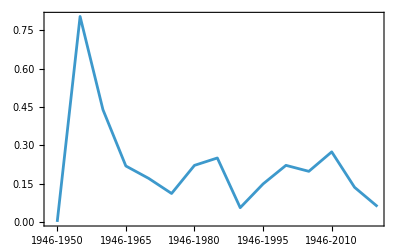
-Graphics-新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）

```mathematica
Labeled[ListPlot[mainMeSHgennewcomercount/mainMeSHflatcountAcm/.Indeterminate->0,Joined->True,PlotRange->Full,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"新規出現主要ディスクリプターの主要ディスクリプターに占める割合（%）"]
```

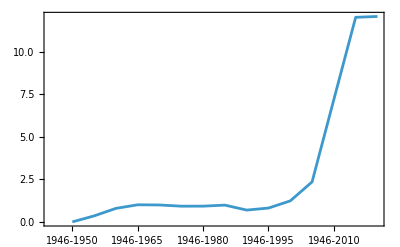
-Graphics-主要ディスクリプターの全出現ディスクリプターに占める割合（%）

```mathematica
Labeled[ListPlot[mainMeSHflatcountAcm/MeSHDesccountAcm*100,Joined->True,Frame->True,FrameTicks->{Automatic,{genticks,None}}],"主要ディスクリプターの全出現ディスクリプターに占める割合（%）"]
```